## Initialisation stuff

```mathematica
$packageDir = "~/Documents/IDrive-Sync/Work/Delft/Projects/Purification/Simulations/QSIM";
Needs["QSIM`basicfunctions`",FileNameJoin[{$packageDir,"QSIM_basicFunctions.m"}]]
Needs["QSIM`measurement`",FileNameJoin[{$packageDir,"QSIM_measurement.m"}]]
Needs["QSIM`stabilizers`",FileNameJoin[{$packageDir,"QSIM_stabilizers.m"}]]
Needs["QSIM`nonlocal`",FileNameJoin[{$packageDir,"QSIM_nonlocal.m"}]]
Needs["QSIM`noise`",FileNameJoin[{$packageDir,"QSIM_noise.m"}]]
Needs["QSIM`superoperators`",FileNameJoin[{$packageDir,"QSIM_superoperators.m"}]]
Needs["QSIM`errorAnalysis`",FileNameJoin[{$packageDir,"QSIM_errorAnalysis.m"}]]
```

#### Partial trace defn:

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

#### ParTrans

```mathematica
permon[n_]:=Flatten[Table[{i,i},{i,n}]+Table[{0,n},{n}]];
permon[n_]:=Flatten[Table[{i,i},{i,n}]+Table[{0,n},{n}]];
transpose[args__] := Module[{},
If[TensorRank[List[args][[1]]] < 2, Return[List[args][[1]]],
Return[Transpose[args]],Print["Error in transpose"] ] ];
oten2nten[otn_]:=transpose[otn,permon[TensorRank[otn]/2]];
prodlist[ls_]:=Product[ls[[i]],{i,Length[ls]}];
nten2mat[ntn_]:=Module[{dims=Dimensions[ntn]},
Partition[ Flatten[ntn] , prodlist[Take[dims,-Length[dims]/2]] ]
	]
oten2mat[otn_]:=nten2mat[oten2nten[otn]];
mat2nten[mt_,ddl_]:=Module[
{ddm=ddl,fmt=Flatten[mt],jm,lnd=Length[ddl]},
		For[jm=1,jm<=lnd,++jm, 
If[  0==Length[ ddm[[jm]] ]  , ddm[[jm]]={ddl[[jm]],ddl[[jm]]}  ];  ];
Fold[ Partition, fmt, Most[Reverse[Flatten[Transpose[ddm]]]] ]];
permno[n_]:=Join[-1+2*Table[i,{i,n}],2*Table[i,{i,n}]];
permtrans[n_,q_]:=Array[If[#==2*q,2*q-1,If[#==(2*q-1),2*q,#]]&,2*n];
nten2oten[ntn_]:=transpose[ntn,permno[TensorRank[ntn]/2]];
mat2oten[mt_,ddl_]:=nten2oten[mat2nten[mt,ddl]];

partrans[mt_,q_,dl_]:=
    oten2mat[transpose[mat2oten[mt,dl],permtrans[Length[dl],q]]]
```

#### Data functions

```mathematica
basePath="/Users/humphreys/Repositories/personal_calcs/Work/Modelling/Purification/MeasuredFidelities";
loadData[theta_]:=Module[{},dataFile=Import[basePath<>"/correlations_for_"<>StringReplace[ToLowerCase[ToString[theta,InputForm]],"/"->""]<>".csv","Table"];
header=dataFile[[1]];
data=dataFile[[3;;-1;;2]];
XXm=data[[;;,2]];
YYm=data[[;;,4]];
ZZm=data[[;;,6]];
XXmu=data[[;;,3]];
YYmu=data[[;;,5]];
ZZmu=data[[;;,7]];
Fidm=data[[;;,14]];
Fidmu=data[[;;,15]];
XXp=data[[;;,8]];
YYp=data[[;;,10]];
ZZp=data[[;;,12]];
XXpu=data[[;;,9]];
YYpu=data[[;;,11]];
ZZpu=data[[;;,13]];
Fidp=data[[;;,16]];
Fidpu=data[[;;,17]];
bins =data[[;;,1]];

binSize=bins[[2]]-bins[[1]];
maxAttempts=bins[[-1]];

XX=1/2(XXm+XXp);
XXu=1/2 √(XXmu^2+XXpu^2);
YY=1/2(YYm+YYp);
YYu=1/2 √(YYmu^2+YYpu^2);

ZZ=1/2(ZZm+ZZp);
ZZu=1/2 √(ZZmu^2+ZZpu^2);

Fid=1/2(Fidm+Fidp);
Fidu=1/2 √(Fidmu^2+Fidpu^2);]
```

## Model

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 

pd - the probability that a photon emitted is detected pd = pZPL*pDetect where: 
	- pZPL - probability that a given photon is in the zero photon line
	- pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>

(or can treat the raw state as being werner state in which case we need only the fidelity: 
fid - The fidelity of the raw state immediately after it is generated if there was no photon loss) 



The parameters of the distillation procedure:

pCNOT - the error rate when a CNOT gate can be performed between electron and nuclear qubits
pSWAP - the error rate when a SWAP operation is performed between electron and nuclear qubits
pmBright - the probability of error in measuring the bright state
pmDark - the probability of error in measureing the dark state
pp - the probability for a phase error between the genration of raw state 1 & 2


-----------------------------------------------
	Additional parameters
-----------------------------------------------
pCarbonDephasing - the probability for a phase error on the stored carbon state
RndOpticalPhase - the phase imprinted on the first raw state (this parameter is only just to check the robustness of the protocol





the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pZPL_,pDetect_,pDC_]:=Module[{p00,p01,p11,pd},
pd = pZPL*pDetect;
p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = 2(Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd+ 2*pDC*(1-pDC)*(1-pd));
p11 = Sin[theta]^4 *((1-pDC)^2*2*(pd *(1-pd)) + 2(1-pDC)*pDC*(1-pd)^2);

{p00,p01,p11}/(p00+p01+p11)
]

rValueAsym[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd1));

{p00,p01,p10,p11}/(p00+p01+p10+p11)
]
```

### Raw state generation

```mathematica
rawState[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[one,one]+rValue[[2]]*0.5*{{1-fz,0,0,0},{0,fz,-vis*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Exp[-ⅈ*RndOpticalPhase],fz,0},{0,0,0,1-fz}}+rValue[[3]]*KP[zero,zero]];

rawStateAsym[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[one,one]+{{(1-fz)(rValue[[2]]+rValue[[3]])/2,0,0,0},{0,rValue[[2]]*fz,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[-ⅈ*RndOpticalPhase],rValue[[3]]*fz,0},{0,0,0,(1-fz)(rValue[[2]]+rValue[[3]])/2}}+rValue[[4]]*KP[zero,zero]];
```

```mathematica
rawStateAsym[Sqrt[0.72],0.99,rValueAsym[π/4,0.0012,0.0006,1*^-7],0.5π]//TableForm
rawStateAsym[Sqrt[0.72],0.99,rValueAsym[π/8,0.0012,0.0006,1*^-7],0.5π]//TableForm
```

0.502245 | 0 | 0 | 0
0 | 0.165084 | 0.-0.198085 ⅈ | 0
0 | 0.+0.198085 ⅈ | 0.330114 | 0
0 | 0 | 0 | 0.00255657

0.150518 | 0 | 0 | 0
0 | 0.281586 | 0.-0.337875 ⅈ | 0
0 | 0.+0.337875 ⅈ | 0.563078 | 0
0 | 0 | 0 | 0.00481839

### EPL protocol

#### Single qubit gates

```mathematica
For[i=1,i≤3,i++,Subscript[σ, i]={pX,pY,pZ}[[i]]]
```

```mathematica
(*Definition of single spin rotations using the qdensity package
Nomenclature:  r followed by a capital letter --> rotation by π around the axis specified by the letter.
			r followed by a lower case letter: rotation by π/2 around the axis specified by that letter
The rotation direction is given by the appended letter m or p*)

{rxp,rXp,ryp,rYp,rzp,rZp}=Table[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
```

#### Controlled qubit gates

```mathematica
(*When experimenting with^13 C spins we currently have two controlled gates in our toolset. The ±x gate and the ±y gate (difference is effectively given by a phaseshift).
These can be modelled by composite actions depending on the projectors Subscript[𝒫, 0] and Subscript[𝒫, 1] for the electronic state*)
```

```mathematica
gmx=KP[zero,rxp]+KP[one,rxm];
gmy=KP[zero,ryp]+KP[one,rym];
```

#### Our sequence

```mathematica
PurificationFullSequence[inputState_,inputState2_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing1_,pCarbonDephasing2_]:=Module[{rawState,rawState1,rawState2,swapGate,purifyGate,state,cz1,cz2,hads,p,swap1,swap2,probSuccess},

rawState = inputState;
state = KP[rawState,zero,zero];  (*Start out with nucleus in 0, electron in inputState*)
swapGate=Simplify[ⅇ^(ⅈ π/4) KP[rym,id].gmx.KP[rxp,id].gmy];(*the state gets swapped onto nuclear spins *)
swap1 = twoQgate[4,1,3,swapGate];
swap2 = twoQgate[4,2,4,swapGate];
state = swap1.state.CT[swap1];
state = swap2.state.CT[swap2];
state = applyGateNoise[state,pSWAP,1,3];
state = applyGateNoise[state,pSWAP,2,4];

(*the electron spins are measured out in the zero state: NB this is post selective *)
rawState1 = measureOutcomeReal[state,{0,0},pmDark];

(* generate another raw pair on the electrons, this time there's some phase shift pp from the first one *)
rawState2 = (1-pp)*inputState2 + pp*KP[pZ,id].inputState2.KP[pZ,id];

(*dephasing of the stored state is modelled symmetrically for both nuclear spins*)
rawState1 = (1-pCarbonDephasing1)(1-pCarbonDephasing2)*rawState1 + pCarbonDephasing1*(1-pCarbonDephasing2)*KP[pZ,id].rawState1.KP[pZ,id]+
pCarbonDephasing2*(1-pCarbonDephasing1)*KP[id,pZ].rawState1.KP[id,pZ]+pCarbonDephasing1*pCarbonDephasing2*KP[pZ,pZ].rawState1.KP[pZ,pZ];
state = KP[rawState2,rawState1];
(*Print[Chop@rawState1//TableForm];
Print[Chop@(KP[had,had].rawState1.KP[had,had])//TableForm];*)
purifyGate=KP[rxp,id].gmx.KP[ryp,id];

cz1=twoQgate[4,1,3,purifyGate];
cz2=twoQgate[4,2,4,purifyGate];

state=cz1.state.CT[cz1];
state=cz2.state.CT[cz2];

state=applyGateNoise[state,pCNOT,1,3];
state=applyGateNoise[state,pCNOT,2,4];
probSuccess=Tr[KP[one,one,id,id]state];
state=measureOutcomeReal[state,{1,1},pmDark];

(*state= KP[pX,id].state.KP[pX,id];*)
(*Print[(Chop[state/Tr[state]])//MatrixForm];*)
{Chop[state/Tr[state]],probSuccess}
]
```

```mathematica
outputStateRotated[theta_,theta2_,pDetect1_,pDetect2_,pDC_,vis_,fz_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing1_,pCarbonDephasing2_,RndOpticalPhase_,PsiPlus_:True]:=Module[{rawstate,rval,rawstate2,rval2},

rval=rValueAsym[theta,pDetect1,pDetect2,pDC];
rval2 = rValueAsym[theta2,pDetect1,pDetect2,pDC];

rawstate = rawStateAsym[vis,fz,rval,RndOpticalPhase];
rawstate2 =If[PsiPlus==True,rawStateAsym[vis,fz,rval2,RndOpticalPhase],rawStateAsym[-vis,fz,rval2,RndOpticalPhase]];

PurificationFullSequence[rawstate,rawstate2,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing1,pCarbonDephasing2]
]
```

## Calculate outputs

```mathematica
corrs[theta_,pCarbonDephasing1_:0.1,pCarbonDephasing2_:0.1,pp_:0.0,RndOpticalPhase_:0.25π,PsiPlus_:True]:=Module[{pCNOT,pSWAP,pmDark,pmBright,vis,fz,pDetect1,pDetect2,pDC,outSt,outStXX,outStYY,XX,YY,ZZ,Fid,rootX,rootY},
(*RndOpticalPhase=0.25π;(*This gives the avg value*)*)
pCNOT=0.05;
pSWAP = 0.1;
pmDark = 0.01;
pmBright = 0.1;
vis =Sqrt[0.72];
fz = 0.99;
pDetect1 = 0.0010;
pDetect2 = 0.0005;
pDC=2*10^-6;

outSt=outputStateRotated[theta,theta,pDetect1,pDetect2,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing1,pCarbonDephasing2,RndOpticalPhase,PsiPlus][[1]];
rootX = MatrixExp[-ⅈ*pX*π/4];
rootY = MatrixExp[-ⅈ*pY*π/4];
outStXX= KP[rootY†,rootY†].outSt.KP[rootY†,rootY†]†;
outStYY= KP[rootX,rootX].outSt.KP[rootX,rootX]†;
(*Print[outStXX//TableForm];
*)
If[PsiPlus==True,
ZZ=(outSt[[1,1]]+outSt[[4,4]]);
XX=Re@(outStXX[[2,2]]+outStXX[[3,3]]);
YY=Re@(outStYY[[1,1]]+outStYY[[4,4]]);
Fid=Re@Fidelity[outSt,bellState[3]];,
ZZ=(outSt[[2,2]]+outSt[[3,3]]);
XX=Re@(outStXX[[2,2]]+outStXX[[3,3]]);
YY=Re@(outStYY[[2,2]]+outStYY[[3,3]]);
Fid=Re@Fidelity[outSt,bellState[2]];];
{2(XX-0.5),2(YY-0.5),2(ZZ-0.5),Fid}(*Returns PARITY*)
]
```

```mathematica
ebits[theta_,pCarbonDephasing1_:0.1,pCarbonDephasing2_:0.1,pp_:0.0,RndOpticalPhase_:0.25π,PsiPlus_:True]:=Module[{pCNOT,pSWAP,pmDark,pmBright,vis,fz,pDetect1,pDetect2,pDC,outSt,outStXX,outStYY,XX,YY,ZZ,Fid,rootX,rootY},
(*RndOpticalPhase=0.25π;(*This gives the avg value*)*)
pCNOT=0.05;
pSWAP = 0.1;
pmDark = 0.01;
pmBright = 0.1;
vis =Sqrt[0.72];
fz = 0.99;
pDetect1 = 0.0010;
pDetect2 = 0.0005;
pDC=2*10^-6;

outSt=outputStateRotated[theta,theta,pDetect1,pDetect2,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing1,pCarbonDephasing2,RndOpticalPhase,PsiPlus][[1]];
Log[2,Total[SingularValueList[partrans[outSt,1,{2,2}]]]]
]
```

```mathematica
FirstClickProb[theta_,pd1_,pd2_,pDC_:0] := (-1+pDC) (-2 pDC Cos[theta]^4+(-4 pDC+pd1 (-1+3 pDC)+pd2 (-1+3 pDC)) Cos[theta]^2 Sin[theta]^2-(pd2+pd1 (1+2 pd2 (-1+pDC)-5 pDC)+2 pDC+2 pd1^2 pDC-pd2 pDC) Sin[theta]^4);

SecondClickProbGivenFirstClick[n_,theta_,pd1_,pd2_,pDC_:0]:=FirstClickProb[theta,pd1,pd2,pDC](1-FirstClickProb[theta,pd1,pd2,pDC])^(n-1);
SecondClickProb[n_,theta_,pd1_,pd2_,pDC_:0,StorageSuccessProb:_1]:=StorageSuccessProb^2 FirstClickProb[theta,pd1,pd2,pDC]^2((1-FirstClickProb[theta,pd1,pd2,pDC])^(n-1));
```

```mathematica
CumProb[nMax_,theta_,pd1_,pd2_,pDC_:0]:=1-(1-(-1+pDC) (-2 pDC Cos[theta]^4+(-4 pDC+pd1 (-1+3 pDC)+pd2 (-1+3 pDC)) Cos[theta]^2 Sin[theta]^2-(pd2+pd1 (1+2 pd2 (-1+pDC)-5 pDC)+2 pDC+2 pd1^2 pDC-pd2 pDC) Sin[theta]^4))^nMax
```

```mathematica
modelRate[theta_,n_,pCarbonDephasing1_:0.1,pCarbonDephasing2_:0.1,pp_:0.0,RndOpticalPhase_:0.25π,PsiPlus_:True]:=Module[{pCNOT,pSWAP,pmDark,pmBright,vis,fz,pDetect1,pDetect2,pDC,outSt,outStXX,outStYY,XX,YY,ZZ,Fid,rootX,rootY,pSuc,LDEelemLength,StorageSuccessProb,pPurificationSuc,clickRate},
(*RndOpticalPhase=0.25π;(*This gives the avg value*)*)
pCNOT=0.05;
pSWAP = 0.10;
pmDark = 0.01;
pmBright = 0.1;
vis =Sqrt[0.72];
fz = 0.99;
pDetect1 = 0.0010;
pDetect2 = 0.0005;
pDC=2*10^-6;
LDEelemLength=7*^-6;
StorageSuccessProb=0.70;
pPurificationSuc=Chop@outputStateRotated[theta,theta,pDetect1,pDetect2,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing1,pCarbonDephasing2,RndOpticalPhase,PsiPlus][[2]];
clickRate=SecondClickProb[n,theta,pDetect1,pDetect2,pDC,StorageSuccessProb]/LDEelemLength;
{pPurificationSuc clickRate,clickRate,pPurificationSuc}
]
```

## Determining key params

#### Single qubit errors

How do probabilities relate to measured taus?

Lets look at an X state, and how it decoheres

```mathematica
initState={{1/2,1/2},{1/2,1/2}};
ρBlochSph[r_]:=(id+r pX)/2
DephasedState[ρ_,pFlip_]:=(1-pFlip)ρ+pFlip pZ.ρ.pZ
Purity[ρ_]:=Tr[MatrixPower[ρ,2]]
FidelityWX=Tr[initState.ρBlochSph[r]]
```

1/2+r/2

```mathematica
DephasedState[initState,pf]//FullSimplify
ρBlochSph[r]/.r->(1-2pf)//Simplify
```

{{1/2,1/2-pf},{1/2-pf,1/2}}

{{1/2,1/2-pf},{1/2-pf,1/2}}

Therefore the Bloch vector length r is equivalent to (1-2p). And so it follows that if r=Exp[-n/tau], p=(1-Exp[-n/tau])/2

```mathematica
(*1-Sum[Binomial[n,2k] p^(2k)(1-p)^(n-2k),{k,0,n/2}]/.p->(1-Exp[-1/tau])/2//FullSimplify Consistent with my previous model. P per single shot is (1-Exp[-1/tau])/2*)
```

```mathematica
PDephased[tau_,n_]:=(1-Exp[-(n/tau)])/2;(*Derived from Sum[Binomial[n,2k] p^(2k)(1-p)^(n-2k),{k,0,n/2}]*)
```

```mathematica
tauDephasingXY=270;
```

#### Two qubit gate errors

```mathematica
initState={{1/2,1/2},{1/2,1/2}};
swapGate=Simplify[ⅇ^(ⅈ π/4) KP[rym,id].gmx.KP[rxp,id].gmy];
purifyGate=KP[rxp,id].gmx.KP[ryp,id];
state = KP[initState,zero];
state = swapGate.state.CT[swapGate];
state = applyGateNoise[applyGateNoise[state,pNoise,1,2],pNoise,1,2];
state=TraceSystem[state,{1}];
state = KP[zero,state];
state = purifyGate.state.CT[purifyGate];
state = applyGateNoise[state,pNoise,1,2];
fid=Fidelity[state,state/.pNoise->0]
```

4 (1/4-(7 pNoise)/15+(32 pNoise^2)/75-(512 pNoise^3)/3375)

```mathematica
Solve[{fid==0.90,pNoise<1},pNoise]
```

{{pNoise→0.0564238}}

#### Phase flips

What about phase flips between the states?

```mathematica
phasePerAttempt=0.05π /Sqrt[3/0.007];
pFlipPerAttempt=Sin[phasePerAttempt]^2;
```

Phase flips are pretty much irrelevant

#### Phase picked up (rnd optical phase)

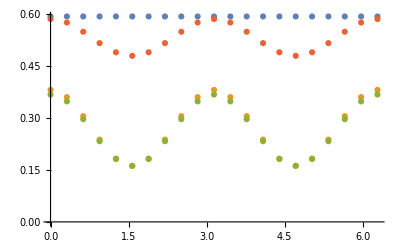

```mathematica
corrsTab=Table[{θ,corrs[π/8,PDephased[tauDephasingXY,400],PDephased[tauDephasingXY,400],0,θ]},{θ,0,2π,π/10}];
ListPlot[Table[{corrsTab[[k,1]],corrsTab[[k,2,i]]},{i,1,4},{k,1,Dimensions[corrsTab][[1]]}]]
```

#### Phase compensation uncertainty

Pick up a slight unknown phase after every attempt since calibration not perfect.

```mathematica
coherences=Integrate[1/(√(2π)Δθ)Exp[-(δθ^2/(2 Δθ^2))] ⅇ^(ⅈ reps δθ),{δθ,-∞,∞},Assumptions->{Δθ>0}]
```

ⅇ^(-1/2 reps^2 Δθ^2)

So block vector length goes as ⅇ^(-1/2 reps^2 Δθ^2), therefore p=(1-ⅇ^(-1/2 n^2 Δθ^2))/2

```mathematica
pLossOfPhase[n_,Δθ_]:=(1-ⅇ^(-1/2 n^2 Δθ^2))/2
```

#### Combining the two processes (phase uncertainty and decoherence)

```mathematica
pCombinedGauss[n_,Δθ_,tau_,tau0_:0]:=(1-ⅇ^(-1/2 n^2 Δθ^2-(n/tau)^2-tau0))/2
pCombinedExp[n_,Δθ_,tau_,tau0_:0]:=(1-ⅇ^(-1/2 n^2 Δθ^2-(n/tau)-tau0))/2
```

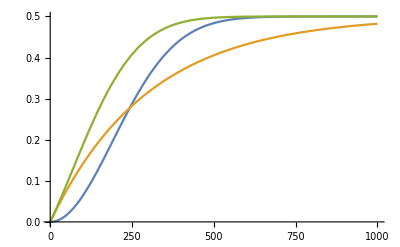

```mathematica
tauDephasingXY=300.; 
phaseUncertaintyPerAttempt =(0.3/180)π;
Plot[{pLossOfPhase[n,phaseUncertaintyPerAttempt],PDephased[tauDephasingXY,n],pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY]},{n,1,1000}]
```

## Comparing with data

#### Modelling functions

```mathematica
Needs["ErrorBarPlots`"]
SetOptions[Plot,BaseStyle->FontSize->13];
SetOptions[ListPlot,BaseStyle->FontSize->14];
```

```mathematica
calculateModel[]:=Module[{},OutcomeCorrs=Table[corrs[theta,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]],{n,1,maxAttempts}];
OutcomeCorrsToPlot=Table[{n,OutcomeCorrs[[n,i]]},{i,1,4},{n,1,maxAttempts}];
binnedOutcomeCorrs=Table[{n,Sum[OutcomeCorrs[[k,i]],{k,n-binSize+1,n}]/binSize},{i,1,3},{n,binSize,maxAttempts,binSize}];
binnedOutcomeFid=Table[{n,Sum[OutcomeCorrs[[k,4]],{k,n-binSize+1,n}]/binSize},{n,binSize,maxAttempts,binSize}];

originalCorrs=ListPlot[OutcomeCorrsToPlot,PlotRange->All,Joined->True,PlotLabel->StringForm["``",theta,InputForm],PlotLegends->{"XX","YY","Fidelity"}];
modelledCorrs=ListPlot[binnedOutcomeCorrs,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Parity for ``, (bins of ``)",theta,binSize,InputForm],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"XX","YY","ZZ"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Parity"}];
modelledFid=ListPlot[binnedOutcomeFid,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Binned attempts","Fidelity"}];]
makeDataPlots[]:=Module[{},XXPlot=ErrorListPlot[Table[{{bins[[i]],XX[[i]]},ErrorBar[XXu[[i]]]},{i,1,Length[XX]}],PlotStyle->ColorData[97,"ColorList"][[1]]];
YYPlot=ErrorListPlot[Table[{{bins[[i]],YY[[i]]},ErrorBar[YYu[[i]]]},{i,1,Length[YY]}],PlotStyle->ColorData[97,"ColorList"][[3]]];
ZZPlot=ErrorListPlot[Table[{{bins[[i]],ZZ[[i]]},ErrorBar[ZZu[[i]]]},{i,1,Length[ZZ]}],PlotStyle->ColorData[97,"ColorList"][[2]]];
FidPlot=ErrorListPlot[Table[{{bins[[i]],Fid[[i]]},ErrorBar[Fidu[[i]]]},{i,1,Length[Fid]}],PlotStyle->ColorData[97,"ColorList"][[1]]];]
```

#### Params

```mathematica
tauDephasingXY=270.; 
phaseUncertaintyPerAttempt =0.35π/180;
1/phaseUncertaintyPerAttempt
Δphase=0.2*π/180
1/Δphase
```

163.702

0.00349066

286.479

### π/4

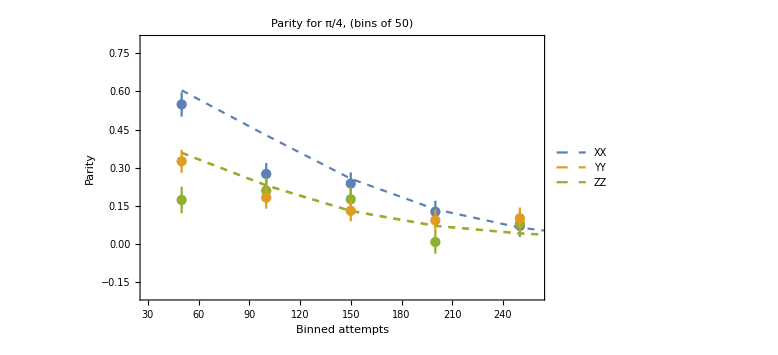

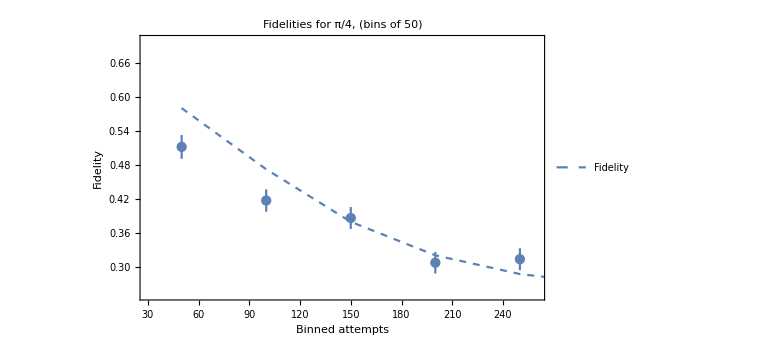

```mathematica
theta =π/4;
loadData[theta];
calculateModel[];
makeDataPlots[];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{{30,260},{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{{30,260},{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

### π/5

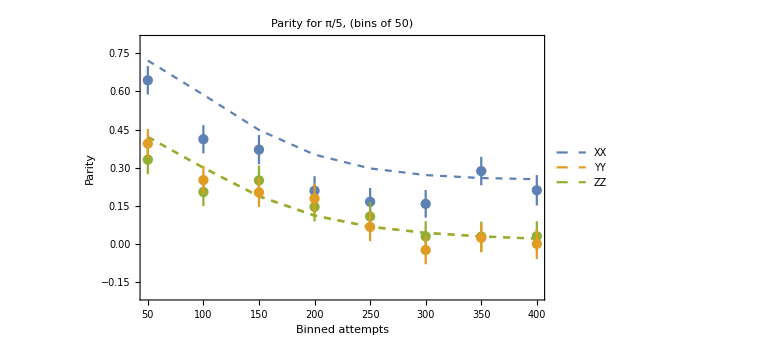

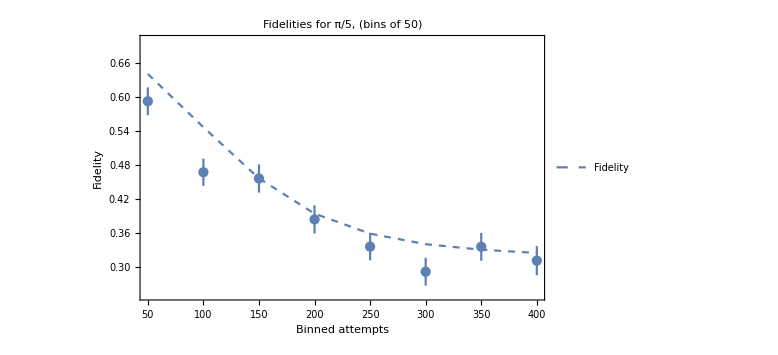

```mathematica
theta =π/5;
loadData[theta];
calculateModel[];
makeDataPlots[];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

### π/6

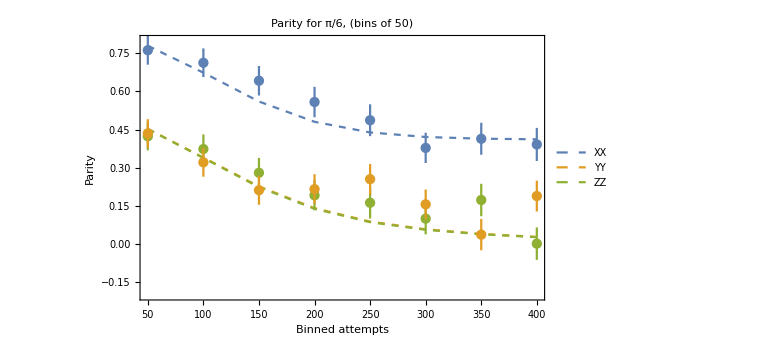

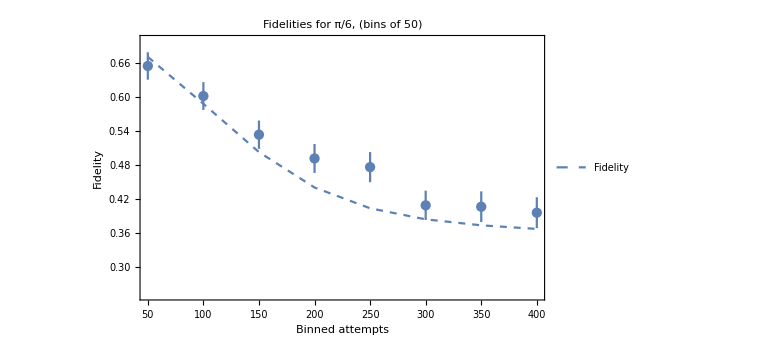

```mathematica
theta =π/6;
loadData[theta];
calculateModel[];
makeDataPlots[];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,0.8}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.7}},AxesOrigin->{0,0.25},ImageSize->Large]
```

### π/8

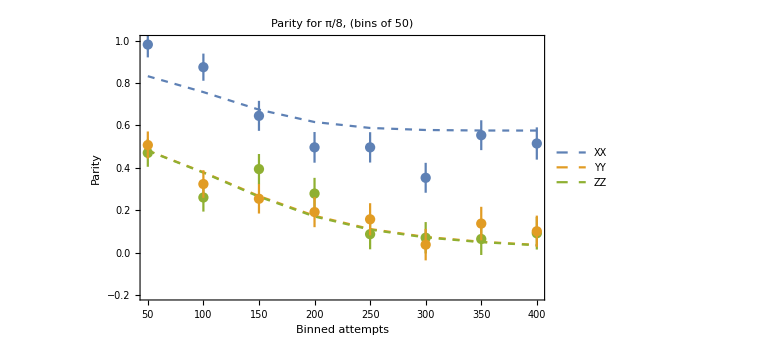

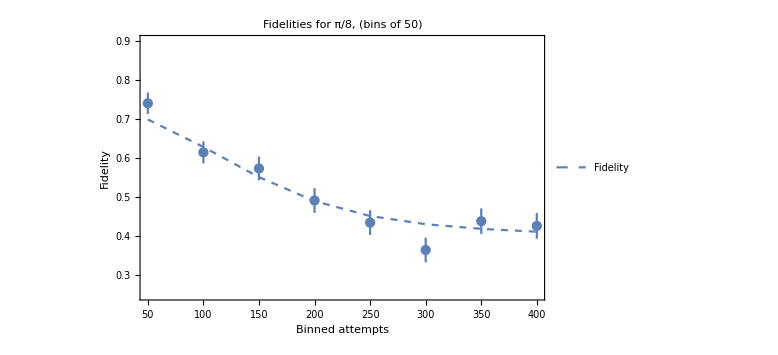

```mathematica
theta =π/8;
loadData[theta];
calculateModel[];
makeDataPlots[];

Show[modelledCorrs,XXPlot,YYPlot,ZZPlot,PlotRange->{Automatic,{-0.2,1.0}},AxesOrigin->{0,0},ImageSize->Large]
Show[modelledFid,FidPlot,PlotRange->{Automatic,{0.25,0.9}},AxesOrigin->{0,0.25},ImageSize->Large]
```

### Function of theta

#### Fidelity

```mathematica
thetas={π/4,π/5,π/6,π/8};
```

```mathematica
FidVsTheta=Table[{Sin[theta]^2,Sum[corrs[theta,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]][[4]],{n,1,binSize}]/binSize},{theta,π/20,π/2,π/20}];
```

```mathematica
Fids={};
Fidsu={};
For[i=1,i≤Dimensions[thetas][[1]],i++,
loadData[thetas[[i]]];
Fids=Append[Fids,Fid[[1]]];
Fidsu=Append[Fidsu,Fidu[[1]]];]
```

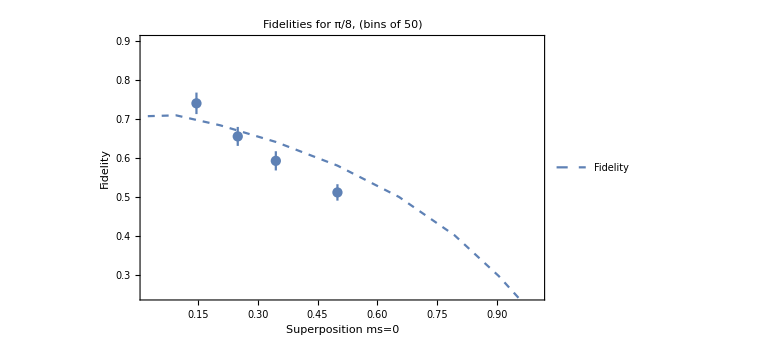

```mathematica
modelledFid=ListPlot[FidVsTheta,PlotRange->All,Joined->True,PlotLabel->Style[StringForm["Fidelities for ``, (bins of ``)",theta,binSize],FontSize->14],PlotStyle->Dashed,PlotLegends->Placed[{"Fidelity"},{Scaled[{0.75,0.9}],Scaled[{0,0.7}]}],Frame->True,FrameLabel->{"Superposition ms=0","Fidelity"}];
FidsPlot=ErrorListPlot[Table[{{Sin[thetas[[i]]]^2,Fids[[i]]},ErrorBar[Fidsu[[i]]]},{i,1,Length[Fids]}],PlotStyle->ColorData[97,"ColorList"][[1]]];

Show[modelledFid,FidsPlot,PlotRange->{Automatic,{0.25,0.9}},AxesOrigin->{0,0.25},ImageSize->Large]
```

#### Ebit rates

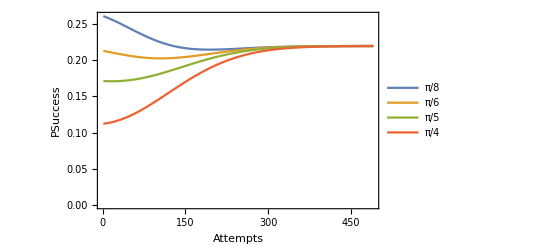

```mathematica
probSuccessVsAttempts=Table[{n,modelRate[theta,n,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]][[3]]},{theta,{π/8,π/6,π/5,π/4}},{n,1,500,10}];
probSuccessVsAttemptsPlot=ListPlot[probSuccessVsAttempts,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Attempts","PSuccess"},PlotLegends->Table[theta,{theta,{π/8,π/6,π/5,π/4}}]]
```

```mathematica
thetas=Table[theta,{theta,{π/8,π/6,π/5,π/4}}];
modelRateVsAttempts=Table[10modelRate[theta,n,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]][[1]],{theta,thetas},{n,1,200,10}];
ebitsVsAttempts=Table[ebits[theta,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]],{theta,thetas},{n,1,200,10}];
ebitsRate=Total[modelRateVsAttempts ebitsVsAttempts,{2}];
```

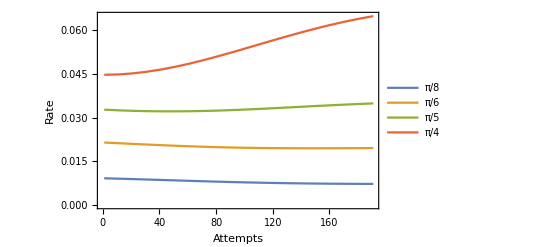

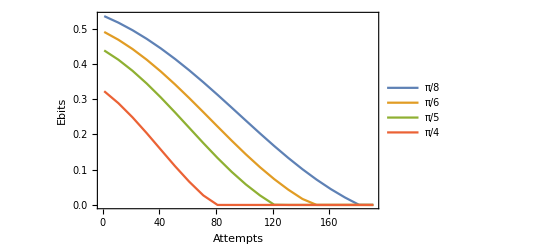

```mathematica
ListPlot[Transpose[Transpose[Join[{Table[n,{theta,thetas},{n,1,200,10}]},{modelRateVsAttempts}],{2,1,3}],{1,3,2}],Joined->True,Frame->True,FrameLabel->{"Attempts","Rate"},PlotLegends->thetas]
ListPlot[Transpose[Transpose[Join[{Table[n,{theta,thetas},{n,1,200,10}]},{ebitsVsAttempts}],{2,1,3}],{1,3,2}],Joined->True,Frame->True,FrameLabel->{"Attempts","Ebits"},PlotLegends->thetas]
```

```mathematica
thetas=Table[theta,{theta,π/20,π/3,π/80}];
modelRateVsAttempts=Table[10modelRate[theta,n,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]][[1]],{theta,thetas},{n,1,250,10}];
ebitsVsAttempts=Table[ebits[theta,pCombinedExp[n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+n,Δphase]],{theta,thetas},{n,1,250,10}];
ebitsRate=Total[modelRateVsAttempts ebitsVsAttempts,{2}];
```

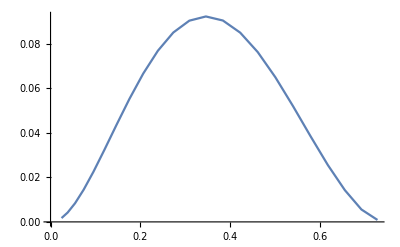

```mathematica
ListPlot[Transpose[Join[{Sin[thetas]^2},{ebitsRate}]],Joined->True]
```

```mathematica
Sin[thetas]^2//N
ebitsRate//N
```

{0.0244717,0.0380602,0.0544967,0.0736799,0.0954915,0.119797,0.146447,0.175276,0.206107,0.238751,0.273005,0.308658,0.345492,0.383277,0.421783,0.46077,0.5,0.53923,0.578217,0.616723,0.654508,0.691342,0.726995}

{0.00171524,0.0041989,0.00836286,0.0144633,0.0225308,0.0323439,0.0434359,0.0551244,0.0665555,0.0768076,0.084981,0.0902961,0.0921844,0.0903651,0.0849169,0.0761971,0.0648926,0.0519372,0.0384232,0.0254953,0.0142381,0.00556886,0.000880181}

#### Binning:

```mathematica
thetas=Table[theta,{theta,π/40,π/3,π/80}];
modelRateVsAttempts=Table[5Sum[modelRate[theta,50(j-1)+n,pCombinedExp[50(j-1)+n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[50(j-1)+n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+50(j-1)+n,Δphase]][[1]],{n,1,50,5}],{theta,thetas},{j,1,500/50}];
ebitsVsAttempts=Table[1/10 Sum[ebits[theta,pCombinedExp[50(j-1)+n,phaseUncertaintyPerAttempt,tauDephasingXY],pCombinedGauss[50(j-1)+n,phaseUncertaintyPerAttempt,tauDephasingXY],pLossOfPhase[143+50(j-1)+n,Δphase]],{n,1,50,5}],{theta,thetas},{j,1,500/50}];
ebitsRate=Total[modelRateVsAttempts ebitsVsAttempts,{2}];
```

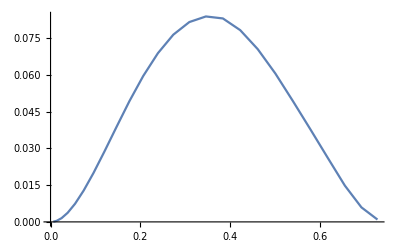

```mathematica
ListPlot[Transpose[Join[{Sin[thetas]^2},{ebitsRate}]],Joined->True]
```

```mathematica
Sin[thetas]^2//N
ebitsRate//N
```

{0.00615583,0.013815,0.0244717,0.0380602,0.0544967,0.0736799,0.0954915,0.119797,0.146447,0.175276,0.206107,0.238751,0.273005,0.308658,0.345492,0.383277,0.421783,0.46077,0.5,0.53923,0.578217,0.616723,0.654508,0.691342,0.726995}

{0.0000665033,0.000445113,0.00151747,0.00371038,0.00739014,0.0127893,0.0199407,0.0286856,0.038628,0.0491955,0.0595095,0.0687988,0.0763501,0.0815032,0.0837846,0.0829756,0.0782026,0.0704476,0.0605007,0.0492008,0.0376386,0.0260446,0.0147977,0.00592599,0.00095985}